# The Lense - Thirring precession in the Hartle - Thorne metric

To describe the geometry around a neutron star we use the Hartle - Thorne metric (Hartle, J . B . & Thorne, K . S . 1968, APJ, 153, 807) and we use relations derived by Abramowicz, M . A ., Almergren, G . J . E ., Kluźniak, W ., & Thampan, A . V . 2003 and Matuszková, M., Török, G., Lančová, D., et al. 2024, A&A, 691, A168.

## The geometry

### The metric

#### The Hartle-Thorne metric

```mathematica
F1=-(8M r^4 (r-2M))^(-1)(u^2(48M^6-8M^5r-24M^4r^2-30M^3r^3-60M^2r^4+135M r^5-45r^6)+(r-M)(16M^5+8M^4r-10M^2r^3-30M r^4+15r^5))+A1;
F2=(8M r(r-2M))^(-1)5(3u^2-1)(r-M)(2M^2+6M r-3r^2)-A1;
G1=(8M r^4 (r-2M))^(-1)(L-72M^5r-3u^2(L-56M^5r))-A1;
L=80M^6+8M^4r^2+10M^3r^3+20M^2r^4-45M r^5+15r^6;
H1=(8M r^4)^(-1)(1-3u^2)(16M^5+8M^4r-10M^2r^3+15M r^4+15r^5)+A2;
H2=(8M r)^(-1)5(1-3u^2)(2M^2-3M r-3r^2)-A2;
A1=15r(r-2M)(1-3u^2)/(16M^2) Log[r/(r-2M)];
A2 =15(r^2-2M^2)(3u^2-1)/(16M^2) Log[r/(r-2M)];
u = Cos[h];

HTmetric=Array[g,{4,4}];
g[1,1]=-(1-2M/r)(1+j^2F1+q F2); g[1,2]=0; g[1,3]=0; g[1,4]=-2M^2/r j  (1-u^2);
g[2,1]=0; g[2,2]=(1-2M/r)^(-1)(1+j^2G1-q F2); g[2,3]=0; g[2,4]=0;
g[3,1]=0; g[3,2]=0; g[3,3]=r^2(1+j^2H1+q H2); g[3,4]=0;
g[4,1]=g[1,4]; g[4,2]=0; g[4,3]=0; g[4,4]=r^2(1-u^2)(1+j^2H1+q H2);

inversemetric=Inverse[HTmetric];

gtt=Simplify[HTmetric[[1,1]]];
gtp=Simplify[HTmetric[[1,4]]];
grr=Simplify[HTmetric[[2,2]]];
ghh=Simplify[HTmetric[[3,3]]];
gpp=Simplify[HTmetric[[4,4]]];

gTT=Simplify[inversemetric[[1,1]]]; 
gTP=Simplify[inversemetric[[1,4]]];
gRR=Simplify[inversemetric[[2,2]]];
gHH=Simplify[inversemetric[[3,3]]];
gPP=Simplify[inversemetric[[4,4]]];
```

#### The Lense-Thirring metric

```mathematica
LTmetric=Array[glt,{4,4}];
glt[1,1]=-(1-2M/r); glt[1,2]=0; glt[1,3]=0; glt[1,4]=-2M^2/r j  (1-u^2);
glt[2,1]=0; glt[2,2]=(1-2M/r)^(-1); glt[2,3]=0; glt[2,4]=0;
glt[3,1]=0; glt[3,2]=0; glt[3,3]=r^2; glt[3,4]=0;
glt[4,1]=glt[1,4];gltg[4,2]=0; glt[4,3]=0; glt[4,4]=r^2(1-u^2);

inverseLTmetric=Inverse[LTmetric];

gttLT=Simplify[LTmetric[[1,1]]];
gtpLT=Simplify[LTmetric[[1,4]]];
grrLT=Simplify[LTmetric[[2,2]]];
ghhLT=Simplify[LTmetric[[3,3]]];
gppLT=Simplify[LTmetric[[4,4]]];

gTTLT=Simplify[inverseLTmetric[[1,1]]]; 
gTPLT=Simplify[inverseLTmetric[[1,4]]];
gRRLT=Simplify[inverseLTmetric[[2,2]]];
gHHLT=Simplify[inverseLTmetric[[3,3]]];
gPPLT=Simplify[inverseLTmetric[[4,4]]];
```

### The orbital angular velocity

```mathematica
Ω=-(gtp + l0 gtt)/(gpp + l0 gtp);
Ω0=Ω/.r->r0;
```

```mathematica
F1om=(48M^7-80M^6r+4M^5r^2-18M^4r^3+40M^3r^4+10M^2r^5+15M r^6-15r^7)(16M^2r^4(r-2M))^(-1)+Aom;
F2om=(5(6M^4-8M^3r-2M^2r^2-3M r^3+3r^4)/(16M^2r(r-2M)))-Aom;
Aom=(15(r^3-2M^3)/(32M^3))Log[r/(r-2M)];
ΩK=(M^(1/2)/r^(3/2))(1-j(M^(3/2)/r^(3/2))+j^2 F1om+q F2om);
ΩK0=ΩK/.r->r0;
```

```mathematica
ΩLT=-(gtpLT + l0LT gttLT)/(gppLT + l0LT gtpLT);
Ω0LT=ΩLT/.r->r0;
```

```mathematica
ΩKLT=M^(1/2)/r^(3/2)-j M^2/r^3;
ΩK0LT=ΩKLT/.r->r0;
```

### The time component of the 4-velocity

```mathematica
uT=1/Sqrt[(-gtt-2 Ω gtp-Ω^2 gpp)];
uT0=uT/.{r-> r0,h->  π/2};
```

```mathematica
uTLT =(1/Sqrt[(-gttLT-2 ΩKLT gtpLT-ΩKLT^2 gppLT)]);
uT0LT=uTLT/.{r-> r0,h->  π/2};
```

### The specific energy

```mathematica
ut = uT(gtt+Ω gtp);
ut0=ut/.{r-> r0, h-> π/2};
```

```mathematica
utLT = Factor[uTLT(gttLT+ΩLT gtpLT)];
ut0LT=utLT/.{r-> r0, h-> π/2};
```

### The effective potential

```mathematica
Ueff=Simplify[(gTT-2 gTP ell + gPP ell^2)] ;
```

```mathematica
UeffLT=Simplify[(gTTLT-2 gTPLT ell + gPPLT ell^2)] ;
```

### The specific angular momentum

```mathematica
L0L=(M^(1/2)r^(3/2))/(r-2M);
F1L=(16M^2r^4(r-2M)^2)^(-1)(96M^8-112M^7r-8M^6r^2-48M^5r^3+42M^4r^4+220M^3r^5-260M^2r^6+105M r^7-15r^8)+AL;
F2L=(16M^2r(r-2M))^(-1)5(6M^4-22M^2r^2+15M r^3-3r^4)+AL;
AL=((15)/(32M^3))(2M^3+4M^2r-4M r^2+r^3)Log[r/(r-2M)];
l=L0L(1-j((M^(3/2)(3r-4M))/(r^(3/2)(r-2M)))+j^2  F1L-q F2L);
l0 = l/.r-> r0;
```

```mathematica
lLT=(M^(1/2)r^(3/2))/(r-2M)-j M^2(3r-4M)/(r-2M)^2;
l0LT= lLT/.r-> r0;
```

```mathematica
ellLT=ell/.Simplify[Solve[D[UeffLT/.h->π/2,r]==0,ell][[1]]];
ell0LT=ellLT/.r->r0;
```

### The epicyclic frequencies

#### The radial epicyclic frequency

```mathematica
F1r=((6M^(3/2)(r+2M))/(r^(3/2)(r-6M)));
F2r=(8M^2r^4(r-2M)(r-6M))^(-1)(384M^8-720M^7r-112M^6r^2-76M^5r^3-138M^4r^4-130M^3r^5+635M^2r^6-375M r^7+60r^8)+Ar;
F3r=((5(48M^5+30M^4r+26M^3r^2-127M^2r^3+75M r^4-12r^5))/(8M^2r(r-2M)(r-6M)))-Ar;
Ar=((15r(r-2M)(2M^2+13M r-4r^2))/(16M^3(r-6M)))Log[r/(r-2M)];
Ωr=Sqrt[M(r-6M)r^(-4)(1+j F1r-j^2 F2r -q F3r)];
```

```mathematica
ΩrLT=Sqrt[M(r-6M)r^(-4)+6j M^2 Sqrt[M r^3](2M +r)r^(-7)];
```

#### The vertical epicyclic frequency

```mathematica
G1v=6M^(3/2)/r^(3/2);
G2v=(8M^2r^4(r-2M))^(-1)(48M^7-224M^6r+28M^5r^2+6M^4r^3-170M^3r^4+295M^2r^5-165M r^6+30r^7)-Bv;
G3v=((5(6M^4+34M^3r-59M^2r^2+33M r^3-6r^4))/(8M^2r(r-2M)))+Bv;
Bv=((15(2r-M)(r-2M)^2)/16M^3)Log[r/(r-2M)];
Ωθ=Sqrt[M r^(-3)(1-j G1v+j^2 G2v +q G3v)];
```

```mathematica
ΩθLT=Sqrt[M r^(-3)-6j M^2Sqrt[M r^3]r^(-6)];
```

### The function of the torus surface

```mathematica
B2 = β^2r0^2 uT0^2 Ω0^2 /2;
f=1-(1-ut0/ut)/B2;
```

```mathematica
kf=f/.{j->0,q->0};
jf=D[f,j]/.{j->0,q->0};
j2f=D[f,{j,2}]/.{j->0,q->0};
qf=D[f,q]/.{j->0,q->0};
linf=kf+j jf+1/2j^2 j2f+q qf;
```

```mathematica
linfLT=kf+j jf;
```

### Some interesting orbits

#### The innermost stable circular orbit

```mathematica
rms=6M(1-j((2/3)Sqrt[2/3])+j^2((251647/2592)-240Log[3/2])+q((-9325/96)+240Log[3/2]));
```

```mathematica
numrms:=r/.FindRoot[Ωr^2==0,{r,rms},AccuracyGoal->3,PrecisionGoal->6]
```

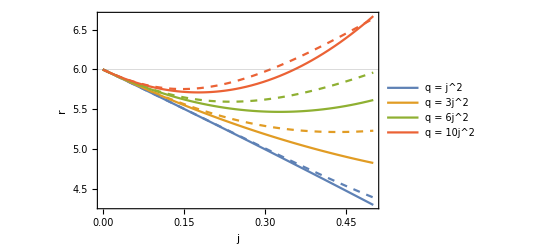

```mathematica
M=1; q=j^2; orbit1=Table[{j,numrms},{j,0,0.5,0.01}];  q=3j^2; orbit2=Table[{j,numrms},{j,0,0.5,0.01}]; q=6j^2; orbit3=Table[{j,numrms},{j,0,0.5,0.01}];  q=10j^2; orbit4=Table[{j,numrms},{j,0,0.5,0.01}]; Clear[j,q];
Show[Plot[{rms/.q->1j^2,rms/.q->3j^2,rms/.q->6j^2,rms/.q->10j^2},{j,0,0.5},PlotStyle->{Line},LabelStyle->Directive[16,FontFamily->"Times New Roman"],GridLines->{None,{6}},Frame->True,Axes->False,FrameLabel->{"j","r"},PlotLegends->{"q = j^2","q = 3j^2","q = 6j^2","q = 10j^2"}],ListLinePlot[{orbit1,orbit2,orbit3,orbit4},PlotStyle->{Dashed}]]
Clear[M]
```

```mathematica
rmsLT=6M-4M j Sqrt[2/3];
```

```mathematica
numrmsLT:=r/.FindRoot[ΩrLT^2==0,{r,rmsLT},AccuracyGoal->3,PrecisionGoal->6]
```

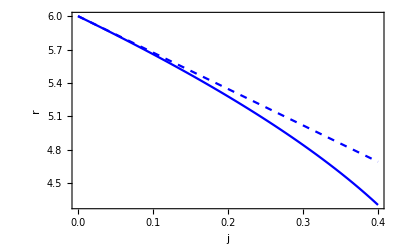

```mathematica
M=1;Plot[{numrmsLT,rmsLT},{j,0,0.4},PlotStyle->{Blue,{Blue,Dashed}},LabelStyle->Directive[16,FontFamily->"Times New Roman"],Frame->True,Axes->False,FrameLabel->{"j","r"}]
Clear[M]
```

#### Marginally bound circular orbit

```mathematica
rmb=4M(1-j(1/2)-j^2((8047/256)-45Log[2])+q((1005/32)-45Log[2]));
```

```mathematica
numrmb:=r0/.FindRoot[ut0+1==0,{r0,rmb},AccuracyGoal->3,PrecisionGoal->6];
```

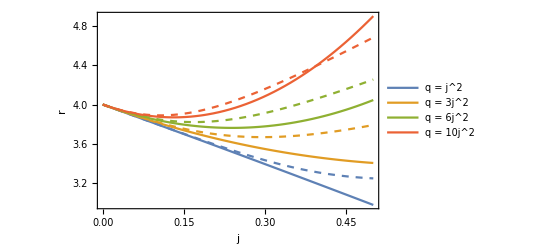

```mathematica
M=1;q=j^2; orbit1=Table[{j,numrmb},{j,0,0.5,0.01}];  q=3j^2; orbit2=Table[{j,numrmb},{j,0,0.5,0.01}]; q=6j^2; orbit3=Table[{j,numrmb},{j,0,0.5,0.01}];  q=10j^2; orbit4=Table[{j,numrmb},{j,0,0.5,0.01}]; Clear[j,q];
Show[Plot[{rmb/.q->1j^2,rmb/.q->3j^2,rmb/.q->6j^2,rmb/.q->10j^2},{j,0,0.5},PlotStyle->{Line},LabelStyle->Directive[16,FontFamily->"Times New Roman"],GridLines->{None,{6}},Frame->True,Axes->False,FrameLabel->{"j","r"},PlotLegends->{"q = j^2","q = 3j^2","q = 6j^2","q = 10j^2"}],ListLinePlot[{orbit1,orbit2,orbit3,orbit4},PlotStyle->{Dashed}]]
Clear[M]
```

```mathematica
rmbLT=4M-2j;
```

```mathematica
numrmbLT:=r0/.FindRoot[ut0LT+1==0,{r0,rmbLT},AccuracyGoal->3,PrecisionGoal->6];
```

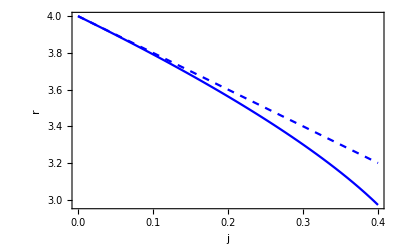

```mathematica
M=1;Plot[{numrmbLT,rmbLT},{j,0,0.4},PlotStyle->{Blue,{Blue,Dashed}},LabelStyle->Directive[16,FontFamily->"Times New Roman"],Frame->True,Axes->False,FrameLabel->{"j","r"}]
Clear[M]
```

#### ν_θ : ν_r = 3 : 1

```mathematica
r31:=r/.FindRoot[Re[Ωθ/Ωr-3],{r,7},AccuracyGoal->3,PrecisionGoal->6]
```

```mathematica
r31LT:=r/.FindRoot[Re[ΩθLT/ΩrLT-3],{r,7},AccuracyGoal->3,PrecisionGoal->6]
```

#### ν_θ : ν_r = 2 : 1

```mathematica
r21:=r/.FindRoot[Re[Ωθ/Ωr-2],{r,8},AccuracyGoal->3,PrecisionGoal->6]
```

```mathematica
r21LT:=r/.FindRoot[Re[ΩθLT/ΩrLT-2],{r,8},AccuracyGoal->3,PrecisionGoal->6]
```

#### ν_θ : ν_r = 3 : 2

```mathematica
r32:=r/.FindRoot[Re[Ωθ/Ωr-3/2],{r,13},AccuracyGoal->3,PrecisionGoal->6]
```

```mathematica
r32LT:=r/.FindRoot[Re[ΩθLT/ΩrLT-3/2],{r,13},AccuracyGoal->3,PrecisionGoal->6]
```

### The maximum torus thickness

#### β_cusp

```mathematica
rc=krc( 1 + j jrc + j^2 j2rc + q qrc);
eqrc=(l/.r->rc)-l0;
keqrc= eqrc/.{j->0,q->0};
jeqrc=D[eqrc,j]/.{j->0,q->0};
j2eqrc=D[eqrc,{j,2}]/.{j->0,q->0};
qeqrc=D[eqrc,q]/.{j->0,q->0};
jc=FullSimplify[Solve[FullSimplify[jeqrc]==0,jrc][[1]],Assumptions->r0>4];
j2c=Simplify[Solve[FullSimplify[j2eqrc]==0,j2rc][[1]],Assumptions->r0>4];
qc=Simplify[Solve[FullSimplify[qeqrc]==0,qrc][[1]],Assumptions->r0>4];
rcusp=rc/.qc/.j2c/.jc;
krc=2r0(r0-1+Sqrt[2r0-3])(r0-2)^(-2);
```

```mathematica
βcusp=Sqrt[2/(Ω0^2 uT0^2 r0^2)  * (1-ut0/ut)/.r->rcusp/.h->Pi/2];
```

```mathematica
numβcusp:=(df=D[linf/.h->Pi/2,r]/.β->0.05; cusp=r/.FindRoot[df==0,{r,3.5},AccuracyGoal->3,PrecisionGoal->6]; fbeta=linf/.{r->cusp,h->Pi/2};β/.FindRoot[fbeta==0,{β,10^(-5)},AccuracyGoal->3,PrecisionGoal->6])
```

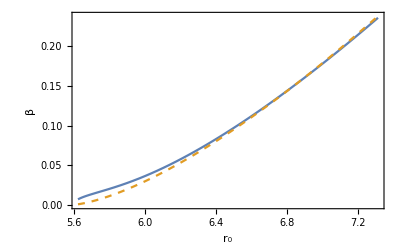

```mathematica
M=1;j=0.3;q=6j^2;r1=numrms;r2=r21;
Plot[{βcusp,numβcusp},{r0,r1,r2},PlotStyle->{Line,Dashed},Frame->True,FrameLabel->{Subscript["r",0],"β"},LabelStyle->Directive[16,FontFamily->"Times New Roman"]]
Clear[j,q,M]
```

```mathematica
rcuspLT=2r0(r0-1+Sqrt[2r0-3])(r0-2)^(-2)+j r0^2(2r0-3)(4-r0(3+Sqrt[2r0-3]))/(Sqrt[2](r0-2)^3(r0(2r0-3)/(r0-1+Sqrt[2r0-3]))^(3/2));
```

```mathematica
βcuspLT=Sqrt[2/(Ω0LT^2 uT0LT^2 r0^2)  * (1-ut0LT/utLT)/.r->rcuspLT/.h->Pi/2];
```

```mathematica
numβcuspLT:=(dfLT=D[linfLT/.h->Pi/2,r]/.β->0.05; cuspLT=r/.FindRoot[dfLT==0,{r,3},AccuracyGoal->3,PrecisionGoal->6]; fbetaLT=linfLT/.{r->cuspLT,h->Pi/2};β/.FindRoot[fbetaLT==0,{β,10^(-5)},AccuracyGoal->3,PrecisionGoal->6])
```

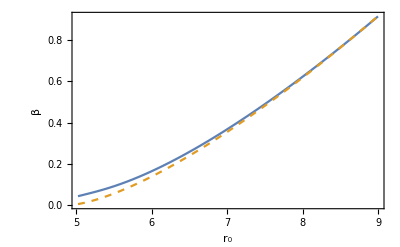

```mathematica
M=1;j=0.3;r1=rmsLT;r2=r32LT;
Plot[{βcuspLT,numβcuspLT},{r0,r1,r2},PlotStyle->{Line,Dashed},Frame->True,FrameLabel->{Subscript["r",0],"β"},LabelStyle->Directive[16,FontFamily->"Times New Roman"]]
Clear[j,M]
```

#### β_maxcusp

```mathematica
rmax:=r0/.FindRoot[l-l0==0/.{r->numrmb,h->Pi/2},{r0,10},AccuracyGoal->3,PrecisionGoal->6]
```

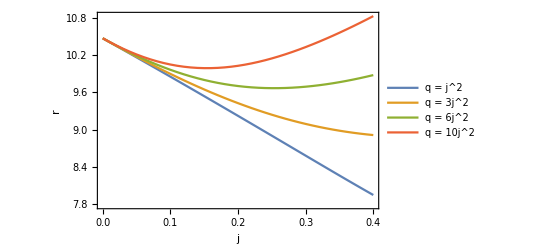

```mathematica
M=1; q=j^2; orbit1=Table[{j,rmax},{j,0,0.4,0.01}];  q=3j^2; orbit2=Table[{j,rmax},{j,0,0.4,0.01}]; q=6j^2; orbit3=Table[{j,rmax},{j,0,0.4,0.01}];  q=10j^2; orbit4=Table[{j,rmax},{j,0,0.4,0.01}]; Clear[j,q,M];
ListLinePlot[{orbit1,orbit2,orbit3,orbit4},LabelStyle->Directive[16,FontFamily->"Times New Roman"],Frame->True,Axes->False,FrameLabel->{"j","r"},PlotLegends->{"q = j^2","q = 3j^2","q = 6j^2","q = 10j^2"}]
```

```mathematica
rinmax:=r/.FindRoot[ut+1/.h->Pi/2,{r,5},AccuracyGoal->3,PrecisionGoal->4]
βmaxim2:=2/(Ω0^2 uT0^2 r0^2)  * (1-ut0/ut)/.r->rinmax/.h->Pi/2;
```

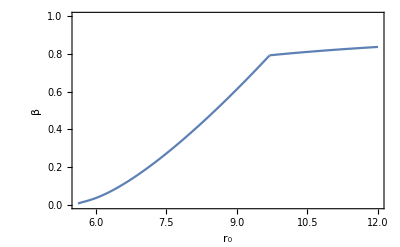

```mathematica
j=0.3;q=6j^2;M=1;r1=numrms;r2=rmax;r3=12;
Show[Plot[βcusp,{r0,r1,r2},PlotRange->{{r1,r3},{0,1}},LabelStyle->Directive[16,FontFamily->"Times New Roman"],Frame->True,Axes->False,FrameLabel->{Subscript["r",0],"β"}],Plot[Sqrt[βmaxim2],{r0,r2,r3}]]
Clear[j,q,M]
```

```mathematica
rmaxLT:=r0/.FindRoot[ellLT-ell0LT/.{r->numrmbLT,h->Pi/2},{r0,11},AccuracyGoal->3]
```

```mathematica
rinmaxLT:=r/.FindRoot[utLT+1/.h->Pi/2,{r,5},AccuracyGoal->3,PrecisionGoal->4]
βmaximLT2:=2/(Ω0LT^2 uT0LT^2 r0^2)  * (1-ut0LT/utLT)/.r->rinmaxLT/.h->Pi/2;
```

## The oscillation frequencies

```mathematica
M=1;c= 2.99792458 10^10 ;G=6.67428 10^(-8) ; Msun=1.98892 10^(33)  ;R=c^3/(G M Msun);
```

### The orbital frequency

```mathematica
νK=ΩK0 R/2/π;  (* ν = R ω/2π, where R is a factor that accounts for the source properties - M, c, G *)
```

```mathematica
νKLT=ΩK0LT R/2/π;
```

### The radial frequency

```mathematica
νR0=(Ωr+m ΩK) R/2/π/.r->r0;
```

```mathematica
νR0LT=(ΩrLT+m ΩKLT) R/2/π/.r->r0;
```

### The vertical frequency

```mathematica
νH0=(Ωθ +m ΩK) R/2/π/.r->r0;
```

```mathematica
νH0LT=(ΩθLT+m ΩKLT) R/2/π/.r->r0;
```

### Plots

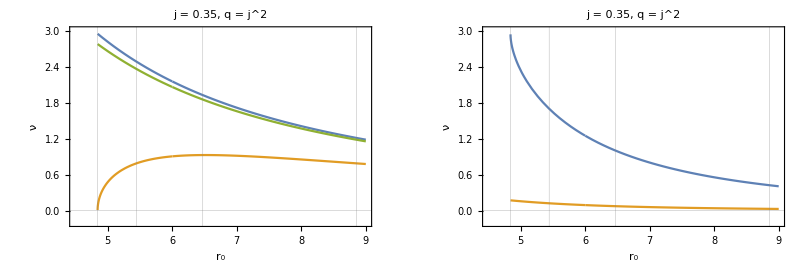

```mathematica
j=0.35;q=j^2;nuk=νK;nur=νR0/.m->0;nuh=νH0/.m->0;nurp=-νR0/.m->-1;nult=-νH0/.m->-1;
r1=numrms;r2=r31;r3=r21;r4=r32;r5=9;
GraphicsRow[{Plot[{nuk/1000,nur/1000,nuh/1000},{r0,r1,r5},PlotRange->{{4.5,9},{-0.2,3}},PlotLabel->"j = 0.35, q = j^2",GridLines->{{r1,r2,r3,r4},{0}},Frame->True,FrameLabel->{Subscript["r",0],"ν"},LabelStyle->Directive[16,FontFamily->"Times New Roman"]],Plot[{nurp/1000,nult/1000},{r0,r1,r5},PlotRange->{{4.5,9},{-0.2,3}},PlotLabel->"j = 0.35, q = j^2",GridLines->{{r1,r2,r3,r4},{0}},Frame->True,FrameLabel->{Subscript["r",0],"ν"},LabelStyle->Directive[16,FontFamily->"Times New Roman"]]}]
Clear[j,q]
```

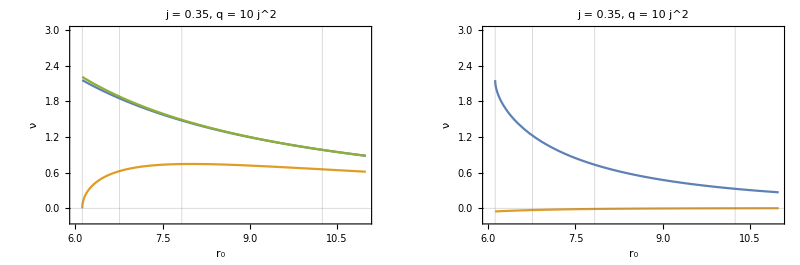

```mathematica
j=0.35;q=10j^2;nuk=νK;nur=νR0/.m->0;nuh=νH0/.m->0;nurp=-νR0/.m->-1;nult=-νH0/.m->-1;
r1=numrms;r2=r31;r3=r21;r4=r32;r5=11;
GraphicsRow[{Plot[{nuk/1000,nur/1000,nuh/1000},{r0,r1,r5},PlotRange->{{6,r5},{-0.2,3}},GridLines->{{r1,r2,r3,r4},{0}},PlotLabel->"j = 0.35, q = 10 j^2",Frame->True,FrameLabel->{Subscript["r",0],"ν"},LabelStyle->Directive[16,FontFamily->"Times New Roman"]],Plot[{nurp/1000,nult/1000},{r0,r1,r5},PlotRange->{{6,r5},{-0.2,3}},PlotLabel->"j = 0.35, q = 10 j^2",GridLines->{{r1,r2,r3,r4},{0}},Frame->True,FrameLabel->{Subscript["r",0],"ν"},LabelStyle->Directive[16,FontFamily->"Times New Roman"]]}]
Clear[j,q]
```

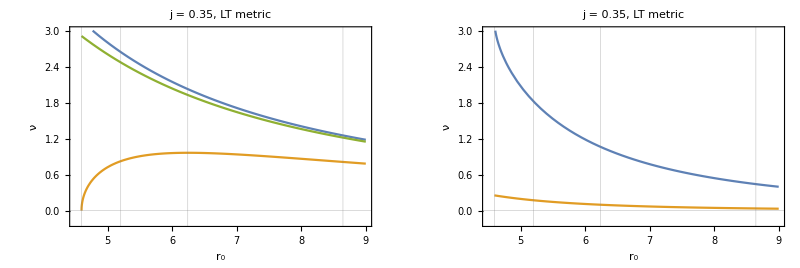

```mathematica
j=0.35;nuk=νKLT;nur=νR0LT/.m->0;nuh=νH0LT/.m->0;nurp=-νR0LT/.m->-1;nult=-νH0LT/.m->-1;
r1=numrmsLT;r2=r31LT;r3=r21LT;r4=r32LT;r5=9;
GraphicsRow[{Plot[{nuk/1000,nur/1000,nuh/1000},{r0,r1,r5},PlotRange->{{4.5,9},{-0.2,3}},GridLines->{{r1,r2,r3,r4},{0}},PlotLabel->"j = 0.35, LT metric",Frame->True,FrameLabel->{Subscript["r",0],"ν"},LabelStyle->Directive[16,FontFamily->"Times New Roman"]],Plot[{nurp/1000,nult/1000},{r0,r1,r5},PlotRange->{{4.5,9},{-0.2,3}},GridLines->{{r1,r2,r3,r4},{0}},Frame->True,PlotLabel->"j = 0.35, LT metric",FrameLabel->{Subscript["r",0],"ν"},LabelStyle->Directive[16,FontFamily->"Times New Roman"]]}]
Clear[j]
```

### The Lense-Thirring frequency of a fluid torus (with pressure corrections)

```mathematica
SetDirectory[NotebookDirectory[]];
cor=ToExpression[Import["correction.txt"]];
corLT=ToExpression[Import["LTcorrection.txt"]];
```

```mathematica
νH=νH0+β^2cor νK/.m->-1;
```

```mathematica
νhcusp=-νH/.β->βcusp;
νltcusp:=Piecewise[{{-νH/.β->numβcusp,r0≤rms+1.5},{-νH/.β->βcusp,r0>rms+1.5}}];
νltmax:=Piecewise[{{νltcusp,r0≤rmax},{-νH/.β^2->βmaxim2,r0>rmax}}];
```

```mathematica
νHLT=νH0LT+β^2corLT νKLT/.m->-1;
```

```mathematica
νhcuspLT=-νHLT/.β->βcuspLT;
νltcuspLT:=Piecewise[{{-νHLT/.β->numβcuspLT,r0≤rmsLT+1.5},{-νHLT/.β->βcuspLT,r0>rmsLT+1.5}}];
νltmaxLT:=Piecewise[{{νltcuspLT,r0≤rmaxLT},{-νHLT/.β^2->βmaximLT2,r0>rmaxLT}}];
```

## The behaviour of Lense-Thirring frequency

#### Lense-Thirring frequency at ISCO

```mathematica
q=1.5j^2;ltisco15={};
For[j=0,j<=0.44,j=j+0.01,r0=numrms;ltisco15=Join[ltisco15,{{j,-νH0/.m->-1}}];Clear[r0]]
Clear[j,q]
```

```mathematica
q=6j^2;ltisco6={};
For[j=0,j<=0.44,j=j+0.01,r0=numrms;ltisco6=Join[ltisco6,{{j,-νH0/.m->-1}}];Clear[r0]]
Clear[j,q]
```

```mathematica
q=10j^2;ltisco10={};
For[j=0,j<=0.44,j=j+0.005,r0=numrms;ltisco10=Join[ltisco10,{{j,-νH0/.m->-1}}];Clear[r0]]
Clear[j,q]
```

```mathematica
ltiscoLT={};
For[j=0,j<=0.44,j=j+0.005,r0=numrmsLT;ltiscoLT=Join[ltiscoLT,{{j,-νH0LT/.m->-1}}];Clear[r0]]
Clear[j]
```

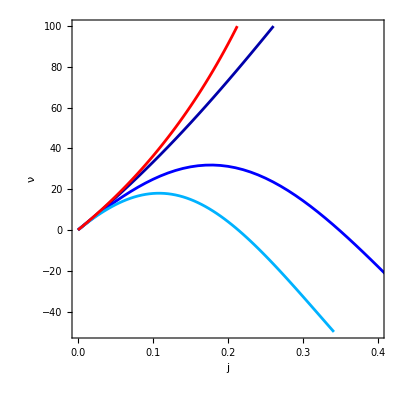

```mathematica
lt0=ListLinePlot[{ltisco15,ltisco6,ltisco10,ltiscoLT},Frame->True,AspectRatio->1,PlotRange->{{0,0.4},{-50,100}},PlotStyle->{Darker[Blue],Blue,Hue[0.55],Red},FrameLabel->{Style["j",FontSlant->Italic],"ν"},LabelStyle->Directive[16,FontFamily->"Times New Roman"]]
```

```mathematica
nult=Table[None,{i,2.5,10,0.5}];nultmax=Table[None,{i,2.5,10,0.5}];
For[x=1,x<=16,x++,q=(2+0.5x) j^2;nult[[x]]={};
For[j=0,j<0.7,j=j+0.002,r0=numrms;
nult[[x]]=Join[nult[[x]],{{j,-νH0/.m->-1}}];Clear[r0]
];Clear[j];
nultmax[[x]]={q/j^2,nult[[x]][[PositionLargest[Table[nult[[x]][[i]][[2]],{i,1,Dimensions[nult[[x]]][[1]]}]]]][[1]][[1]]}
]
Clear[j,q,x]
```

FittedModel[…]

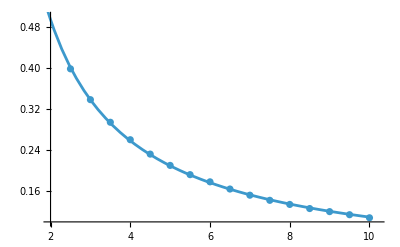

```mathematica
nlm=NonlinearModelFit[nultmax,a x^b,{a,b},x]
Show[ListPlot[nultmax,PlotRange->{{2,10.2},{0.1,0.50}}],Plot[nlm[x],{x,1,10}]]
```

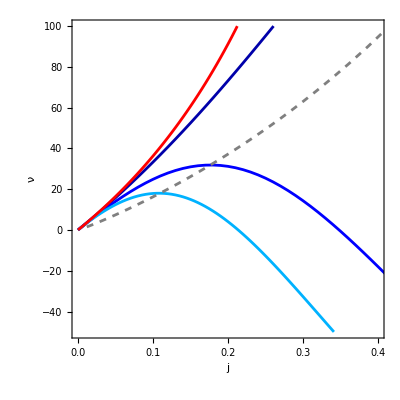

```mathematica
radisco=Ωr^2/.q->x j^2/.j->nlm[x];r00:=r/.FindRoot[radisco,{r,5.5},AccuracyGoal->3];
frek:=-νH0/.m->-1/.r0->r00/.q->x j^2/.j->nlm[x];
tab=Table[{nlm[x],frek},{x,1,200,0.2}];
ltisco=Show[lt0,ListLinePlot[tab,PlotRange->All,PlotStyle->{Gray,Dashed}]]
```

#### Lense-Thirring frequency at r_3:1

```mathematica
q=1.5j^2;lt31015=lt31cusp15={};
For[j=0,j<=0.44,j=j+0.01,r0=r31; lt31015=Join[lt31015,{{j,-νH0/.m->-1}}]; lt31cusp15=Join[lt31cusp15,{{j,νhcusp}}]; Clear[r0]]
Clear[j,q,m,r0]
```

```mathematica
q=6j^2;lt3106=lt31cusp6={};
For[j=0,j<=0.44,j=j+0.01,r0=r31; lt3106=Join[lt3106,{{j,-νH0/.m->-1}}]; lt31cusp6=Join[lt31cusp6,{{j,νhcusp}}]; Clear[r0]]
Clear[j,q,m,r0]
```

```mathematica
q=10j^2;lt31010=lt31cusp10={};
For[j=0,j<=0.44,j=j+0.01,r0=r31; lt31010=Join[lt31010,{{j,-νH0/.m->-1}}]; lt31cusp10=Join[lt31cusp10,{{j,νhcusp}}]; Clear[r0]]
Clear[j,q,m,r0]
```

```mathematica
lt310LT=lt31cuspLT={};
For[j=0,j<=0.44,j=j+0.01,r0=r31LT; lt310LT=Join[lt310LT,{{j,-νH0LT/.m->-1}}]; lt31cuspLT=Join[lt31cuspLT,{{j,νhcuspLT}}]; Clear[r0]]
Clear[j,q,m,r0]
```

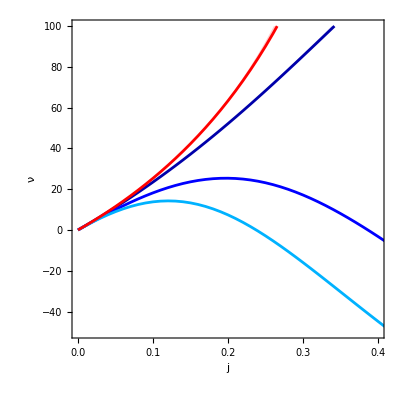

```mathematica
lt31=ListLinePlot[{lt31015,lt3106,lt31010,lt310LT,lt31cusp15,lt31cusp6,lt31cusp10,lt31cuspLT},Frame->True,AspectRatio->1,PlotRange->{{0,0.4},{-50,100}},PlotStyle->{Darker[Blue],Blue,Hue[0.55],Red,None,None,None,None},Filling->{1->{5},2->{6},3->{7},4->{8}},FrameLabel->{Style["j",FontSlant->Italic],"ν"},LabelStyle->Directive[16,FontFamily->"Times New Roman"]]
```

#### Lense-Thirring frequency at r_2:1

```mathematica
q=1.5j^2;lt21015=lt21cusp15={};
For[j=0,j<=0.44,j=j+0.01,r0=r21; lt21015=Join[lt21015,{{j,-νH0/.m->-1}}]; lt21cusp15=Join[lt21cusp15,{{j,νhcusp}}]; Clear[r0]]
Clear[j,q,m,r0]
```

```mathematica
q=6j^2;lt2106=lt21cusp6={};
For[j=0,j<=0.44,j=j+0.01,r0=r21; lt2106=Join[lt2106,{{j,-νH0/.m->-1}}]; lt21cusp6=Join[lt21cusp6,{{j,νhcusp}}]; Clear[r0]]
Clear[j,q,m,r0]
```

```mathematica
q=10j^2;lt21010=lt21cusp10={};
For[j=0,j<=0.44,j=j+0.01,r0=r21; lt21010=Join[lt21010,{{j,-νH0/.m->-1}}]; lt21cusp10=Join[lt21cusp10,{{j,νhcusp}}]; Clear[r0]]
Clear[j,q,m,r0]
```

```mathematica
lt210LT=lt21cuspLT={};
For[j=0,j<=0.44,j=j+0.01,r0=r21LT; lt210LT=Join[lt210LT,{{j,-νH0LT/.m->-1}}]; lt21cuspLT=Join[lt21cuspLT,{{j,νhcuspLT}}]; Clear[r0]]
Clear[j,q,m,r0]
```

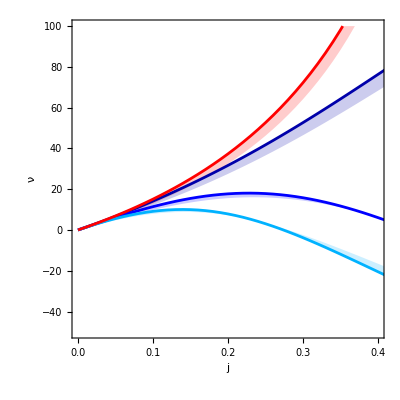

```mathematica
lt21=ListLinePlot[{lt21015,lt2106,lt21010,lt210LT,lt21cusp15,lt21cusp6,lt21cusp10,lt21cuspLT},Frame->True,AspectRatio->1,PlotRange->{{0,0.4},{-50,100}},PlotStyle->{Darker[Blue],Blue,Hue[0.55],{Red},None,None,None,None},Filling->{1->{5},2->{6},3->{7},4->{8}},FrameLabel->{Style["j",FontSlant->Italic],"ν"},LabelStyle->Directive[16,FontFamily->"Times New Roman"]]
```

#### Lense-Thirring frequency at r_3:2

```mathematica
q=1.5j^2;lt32015={};lt32cusp15={};
For[j=0,j<=0.41,j=j+0.01,r0=r32; lt32015=Join[lt32015,{{j,-νH0/.m->-1}}]; lt32cusp15=Join[lt32cusp15,{{j,-νH/.β^2->βmaxim2}}]; Clear[r0]]
Clear[j,q,m,r0]
```

```mathematica
q=6j^2;lt3206={};lt32cusp6={};
For[j=0,j<=0.41,j=j+0.01,r0=r32; lt3206=Join[lt3206,{{j,-νH0/.m->-1}}]; lt32cusp6=Join[lt32cusp6,{{j,-νH/.β^2->βmaxim2}}]; Clear[r0]]
Clear[j,q,m,r0]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
q=10j^2;lt32010={};lt32cusp10={};
For[j=0,j<=0.41,j=j+0.01,r0=r32; lt32010=Join[lt32010,{{j,-νH0/.m->-1}}]; lt32cusp10=Join[lt32cusp10,{{j,-νH/.β^2->βmaxim2}}]; Clear[r0]]
Clear[j,q,m,r0]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
lt320LT={};lt32cuspLT={};
For[j=0,j<=0.41,j=j+0.01,r0=r32LT; lt320LT=Join[lt320LT,{{j,-νH0LT/.m->-1}}]; lt32cuspLT=Join[lt32cuspLT,{{j,-νHLT/.β^2->βmaximLT2}}]; Clear[r0]]
Clear[j,m,r0]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

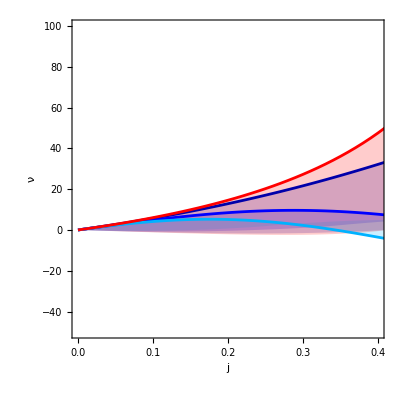

```mathematica
lt32=ListLinePlot[{lt32015,lt3206,lt32010,lt320LT,lt32cusp15,lt32cusp6,lt32cusp10,lt32cuspLT},Frame->True,AspectRatio->1,PlotRange->{{0,0.4},{-50,100}},PlotStyle->{Darker[Blue],Blue,Hue[0.55],Red,None,None,None,None},Filling->{1->{5},2->{6},3->{7},4->{8}},FrameLabel->{Style["j",FontSlant->Italic],"ν"},LabelStyle->Directive[16,FontFamily->"Times New Roman"]]
```

#### Plots

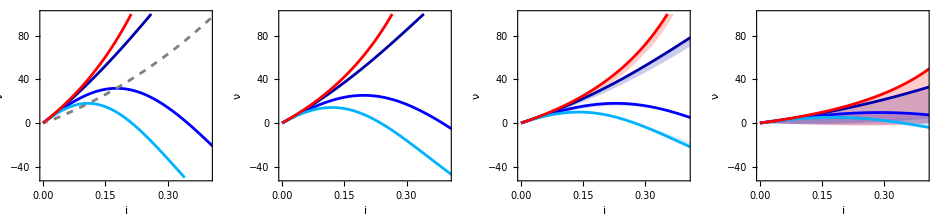

```mathematica
GraphicsRow[{ltisco,lt31,lt21,lt32}]
```

#### Maximum Lense-Thirring frequency

```mathematica
max15=max6=max10=maxLT={};
For[j=0.001,j<=0.41,j=j+0.01,
q=1.5j^2; r1=numrms; max=FindMaximum[{Abs[νH0/.m->-1],r0>=r1},{r0,r1+0.5}]; max15=Join[max15,{{j,max[[1]]}}];
q=6j^2; r1=numrms; max=FindMaximum[{Abs[νH0/.m->-1],r0>=r1},{r0,r1+0.5}]; max6=Join[max6,{{j,max[[1]]}}];
q=10j^2; r1=numrms; max=FindMaximum[{Abs[νH0/.m->-1],r0>=r1},{r0,r1+0.5}]; max10=Join[max10,{{j,max[[1]]}}];
r1=numrmsLT; max=FindMaximum[{Abs[νH0LT/.m->-1],r0>=r1},{r0,r1+0.5}]; maxLT=Join[maxLT,{{j,max[[1]]}}];
]
Clear[j,q]
```

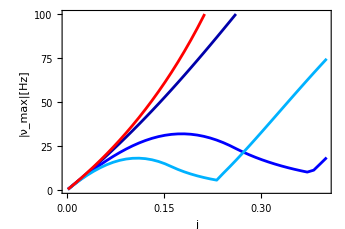

```mathematica
maximum=ListLinePlot[{max15,max6,max10,maxLT},Frame->True,AspectRatio->2/3,PlotRange->{{0,0.4},{0,100}},PlotStyle->{Darker[Blue],Blue,Hue[0.55],Red},FrameLabel->{"j","|ν_max|[Hz]"},LabelStyle->Directive[16,FontFamily->"Times New Roman"]]
```

#### Average Lense-Thirring frequency

```mathematica
ave21015=ave2106=ave21010=ave210LT={};
For[j=0.001,j<=0.41,j=j+0.01,
q=1.5j^2; r1=numrms; r2=r21; ave=NIntegrate[Abs[νH0/.m->-1],{r0,r1,r2}]/(r2-r1); ave21015=Join[ave21015,{{j,ave}}];
q=6j^2; r1=numrms; r2=r21; ave=NIntegrate[Abs[νH0/.m->-1],{r0,r1,r2}]/(r2-r1); ave2106=Join[ave2106,{{j,ave}}];
q=10j^2; r1=numrms; r2=r21; ave=NIntegrate[Abs[νH0/.m->-1],{r0,r1,r2}]/(r2-r1); ave21010=Join[ave21010,{{j,ave}}];
r1=rmsLT; r2=r21LT; ave=NIntegrate[Abs[νH0LT/.m->-1],{r0,r1,r2}]/(r2-r1); ave210LT=Join[ave210LT,{{j,ave}}];
]
Clear[j,q]
```

```mathematica
q=1.5j^2;ave21cusp15={};
For[j=0.001,j<=0.41,j=j+0.02,r1=numrms+0.001;r2=r21;nu=Table[{r0,Abs[νltcusp]},{r0,r1,r2,0.01}];
(*Print[Show[ListLinePlot[nu,PlotStyle->{Gray,Dashed}],Plot[Abs[νH0/.m->-1],{r0,r1,r2}]]];*)
suma=Total[Table[(nu[[i]][[2]]+nu[[i+1]][[2]] )/2*0.01,{i,1,Dimensions[nu][[1]]-1}]]; ave=suma/(r2-r1); ave21cusp15=Join[ave21cusp15,{{j,ave}}]
]
Clear[j,q]
```

```mathematica
q=6j^2;ave21cusp6={};
For[j=0.001,j<=0.41,j=j+0.01,r1=numrms+0.001;r2=r21;nu=Table[{r0,Abs[νltcusp]},{r0,r1,r2,0.01}];
(*Print[Show[ListLinePlot[nu,PlotStyle->{Gray,Dashed}],Plot[Abs[νH0/.m->-1],{r0,r1,r2}]]];*)
suma=Total[Table[(nu[[i]][[2]]+nu[[i+1]][[2]] )/2*0.01,{i,1,Dimensions[nu][[1]]-1}]];ave=suma/(r2-r1);ave21cusp6=Join[ave21cusp6,{{j,ave}}]
]
Clear[j,q]
```

```mathematica
q=10j^2;ave21cusp10={};
For[j=0.001,j<=0.41,j=j+0.01,r1=numrms+0.001;r2=r21;nu=Table[{r0,Abs[νltcusp]},{r0,r1,r2,0.01}];
(*Print[Show[ListLinePlot[nu,PlotStyle->{Gray,Dashed}],Plot[Abs[νH0/.m->-1],{r0,r1,r2}]]];*)
suma=Total[Table[(nu[[i]][[2]]+nu[[i+1]][[2]] )/2*0.01,{i,1,Dimensions[nu][[1]]-1}]]; ave=suma/(r2-r1); ave21cusp10=Join[ave21cusp10,{{j,ave}}]
]
Clear[j,q]
```

```mathematica
ave21cuspLT={};
For[j=0.001,j<=0.41,j=j+0.02,r1=rmsLT+0.01;r2=r21LT;nu=Table[{r0,νltcuspLT(*Abs[νH0LT/.m->-1]*)},{r0,r1,r2,0.01}];
(*Print[Show[ListLinePlot[nu,PlotStyle->{Gray,Dashed}],Plot[Abs[νH0LT/.m->-1],{r0,r1,r2}]]];*)
suma=Total[Table[(nu[[i]][[2]]+nu[[i+1]][[2]] )/2*0.01,{i,1,Dimensions[nu][[1]]-1}]]; ave=suma/(r2-r1); ave21cuspLT=Join[ave21cuspLT,{{j,ave}}]
]
Clear[j]
```

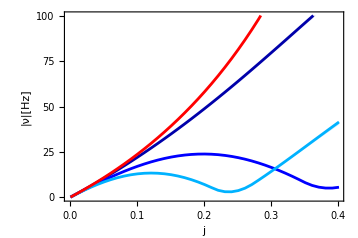

```mathematica
lt21plt=ListLinePlot[{ave21015,ave2106,ave21010,ave210LT,ave21cusp15,ave21cusp6,ave21cusp10,ave21cuspLT},Frame->True,AspectRatio->2/3,PlotRange->{{0,0.4},{0,100}},PlotStyle->{Darker[Blue],Blue,Hue[0.55],Red,None,None,None,None},FrameLabel->{"j","|ν|[Hz]"},Filling->{1->{5},2->{6},3->{7},4->{8}},LabelStyle->Directive[16,FontFamily->"Times New Roman"]]
```

```mathematica
ave32015=ave3206=ave32010=ave320LT={};
For[j=0.001,j<=0.41,j=j+0.01,
q=1.5j^2; r1=numrms; r2=r32; ave=NIntegrate[Abs[νH0/.m->-1],{r0,r1,r2}]/(r2-r1); ave32015=Join[ave32015,{{j,ave}}];
q=6j^2; r1=numrms; r2=r32; ave=NIntegrate[Abs[νH0/.m->-1],{r0,r1,r2}]/(r2-r1); ave3206=Join[ave3206,{{j,ave}}];
q=10j^2; r1=numrms; r2=r32; ave=NIntegrate[Abs[νH0/.m->-1],{r0,r1,r2}]/(r2-r1); ave32010=Join[ave32010,{{j,ave}}];
r1=rmsLT; r2=r32LT; ave=NIntegrate[Abs[νH0LT/.m->-1],{r0,r1,r2}]/(r2-r1); ave320LT=Join[ave320LT,{{j,ave}}];
]
Clear[j,q]
```

```mathematica
q=1.5j^2;ave32cusp15={};
For[j=0.001,j<=0.41,j=j+0.01,r1=numrms+0.001;r2=r32;nu=Table[{r0,Abs[νltmax]},{r0,r1,r2,0.02}];
(*Print[Show[ListLinePlot[nu,PlotStyle->{Gray,Dashed}],Plot[Abs[νH0/.m->-1],{r0,r1,r2}]]];*)
suma=Total[Table[(nu[[i]][[2]]+nu[[i+1]][[2]] )/2*0.02,{i,1,Dimensions[nu][[1]]-1}]]; ave=suma/(r2-r1); ave32cusp15=Join[ave32cusp15,{{j,ave}}]
]
Clear[j,q]
```

```mathematica
q=6j^2;ave32cusp6={};
For[j=0.001,j<=0.41,j=j+0.01,r1=numrms+0.001;r2=r32;nu=Table[{r0,Abs[νltmax]},{r0,r1,r2,0.02}];
(*Print[Show[ListLinePlot[nu,PlotStyle->{Gray,Dashed}],Plot[Abs[νH0/.m->-1],{r0,r1,r2}]]];*)
suma=Total[Table[(nu[[i]][[2]]+nu[[i+1]][[2]] )/2*0.02,{i,1,Dimensions[nu][[1]]-1}]]; ave=suma/(r2-r1); ave32cusp6=Join[ave32cusp6,{{j,ave}}]
]
Clear[j,q]
```

```mathematica
q=10j^2;ave32cusp10={};
For[j=0.001,j<=0.41,j=j+0.01,r1=numrms+0.001;r2=r32;nu=Table[{r0,Abs[νltmax]},{r0,r1,r2,0.02}];
(*Print[Show[ListLinePlot[nu,PlotStyle->{Gray,Dashed}],Plot[Abs[νH0/.m->-1],{r0,r1,r2}]]];*)
suma=Total[Table[(nu[[i]][[2]]+nu[[i+1]][[2]] )/2*0.02,{i,1,Dimensions[nu][[1]]-1}]]; ave=suma/(r2-r1); ave32cusp10=Join[ave32cusp10,{{j,ave}}]
]
Clear[j,q]
```

```mathematica
ave32cuspLT={};
For[j=0.001,j<=0.41,j=j+0.01,r1=rmsLT+0.001;r2=r32LT;nu=Table[{r0,Abs[νltmaxLT]},{r0,r1,r2,0.02}];
(*Print[Show[ListLinePlot[nu,PlotStyle->{Gray,Dashed}],Plot[Abs[νH0LT/.m->-1],{r0,r1,r2}]]];*)
suma=Total[Table[(nu[[i]][[2]]+nu[[i+1]][[2]] )/2*0.02,{i,1,Dimensions[nu][[1]]-1}]]; ave=suma/(r2-r1); ave32cuspLT=Join[ave32cuspLT,{{j,ave}}]
]
Clear[j]
```

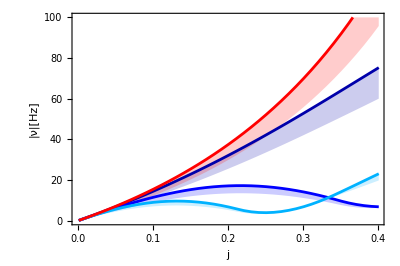

```mathematica
lt32plt=ListLinePlot[{ave32015,ave3206,ave32010,ave320LT,ave32cusp15,ave32cusp6,ave32cusp10,ave32cuspLT},Frame->True,AspectRatio->2/3,PlotRange->{{0,0.4},{0,100}},PlotStyle->{Darker[Blue],Blue,Hue[0.55],Red,None,None,None,None},FrameLabel->{"j","|ν|[Hz]"},Filling->{1->{5},2->{6},3->{7},4->{8}},LabelStyle->Directive[16,FontFamily->"Times New Roman"]]
```